Since we analyze the l=0 case the Spherical Bessel Function for l=0 
is the Sinx/x function. To get the spectrum one needs to solve
J_l(k R) = 0 where R is the end point of our grid. Then 
k = n π / R

```mathematica
RN=10;
k=Table[2 n π/RN,{n,1,21}]//N
```

{0.628319,1.25664,1.88496,2.51327,3.14159,3.76991,4.39823,5.02655,5.65487,6.28319,6.9115,7.53982,8.16814,8.79646,9.42478,10.0531,10.6814,11.3097,11.9381,12.5664,13.1947}

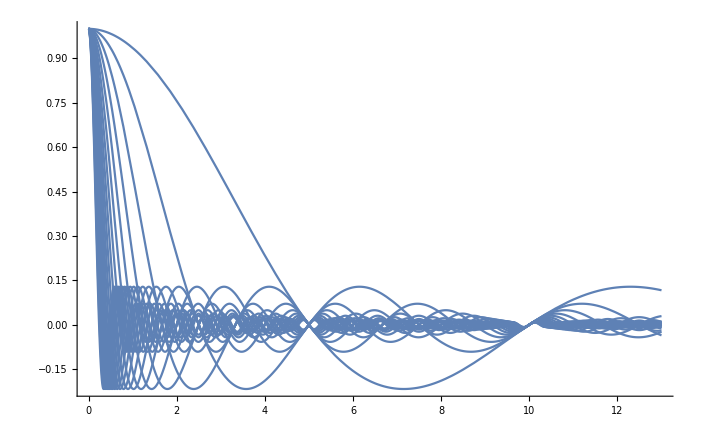

```mathematica
Plot[SphericalBesselJ[0,k x],{x,0,13},PlotRange->All,AspectRatio->1/GoldenRatio]
```

```mathematica
λ = -k^2
```

{-0.394784,-1.57914,-3.55306,-6.31655,-9.8696,-14.2122,-19.3444,-25.2662,-31.9775,-39.4784,-47.7689,-56.8489,-66.7185,-77.3777,-88.8264,-101.065,-114.093,-127.91,-142.517,-157.914,-174.1}

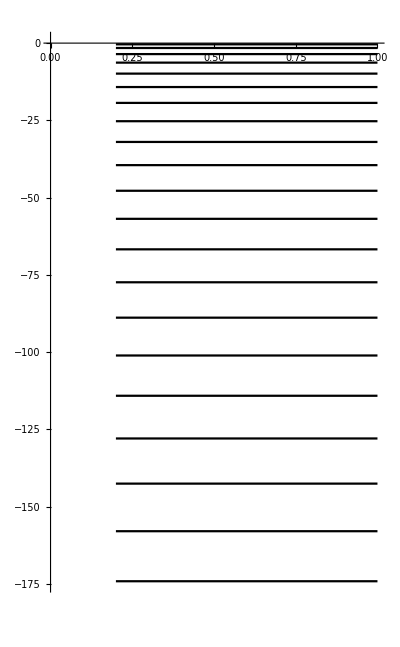

```mathematica
Plot[λ,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}]
```